# 1D linear stability analysis (LSA) phase diagrams for the skeleton and switch models

Parameters transformed to the 1+1D geometry by bulk-boundary ratio of a cylinder of radius 0.5μm

```mathematica
paramsSwitch={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->1*4,
kdD->0.005*4,
kdEr->1.5*4,
kdEl->10^-5*2*4,
kde->1,
λ->5,
μ->20
};
```

Parameters from Halatek, Frey, Cell Reports 2012 @ 37°C
The nonlinear reaction rates are scaled to shift the MinD and MinE concentrations of the pattern-forming region to comparable values as in the switch model

```mathematica
paramsSkeletonScaled={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.013,
Dde->0.013,
kD->0.1*4,
kdD->0.108*4/30,
kdEr->0.435*4/30,
kdEl->0.435*4/30,
kde->0.4*Exp[-Quantity[16.7,"ThermochemicalKilocalories"/"Moles"]/(Quantity["MolarGasConstant"] UnitConvert@Quantity[37,"DegreesCelsius"])+Quantity[16.7,"ThermochemicalKilocalories"/"Moles"]/(Quantity["MolarGasConstant"] UnitConvert@Quantity[20,"DegreesCelsius"])],
λ->6,
μ->100
};
```

## Setup

Setup the reaction terms for the 1+1D switch model

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
-μ cEr+kde mde-kdEr md cEr,
μ cEr-kdEl md cEl,
(kD+kdD md)cDT-kdEr md cEr-kdEl md cEl,
kdEr md cEr+kdEl md cEl-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,5,6}]]
Simplify[Total@f[[{3,4,6}]]]
```

0

0

## Homogeneous fixed point(s)

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cEr+cEl+mde}/.params,{cDD,cDT,cEr,cEl,md,mde}];
Select[{cDD,cDT,cEr,cEl,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cEr,
-DE q^2 cEl ,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cEr,cEl,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cEr,cEl,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS
}
];
```

## LSA

### Switch model

```mathematica
Monitor[sweepLSASwitch=Table[
{
rho,
testInstab[Join[{rhoD->rho[[1]]/4,rhoE->rho[[2]]/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]]]
},{rho,Flatten[Outer[List,10^Range[2,4.5,0.01],10^Range[2,4.5,0.01]],1]}];,rho]
```

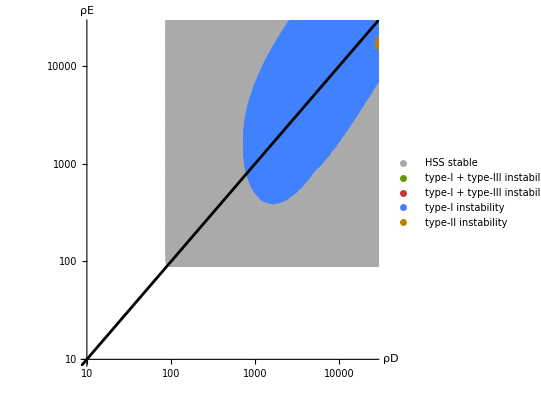

```mathematica
Show[ListLogLogPlot[DeleteCases[{{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==0&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==1&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==2&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==3&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==4&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==5&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,1]]==6&]},{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"ρD","ρE"}),
AspectRatio->1,TicksStyle->Directive[14],
AxesStyle->Thickness[0.002],
PlotRange->{{10,25000},{10,25000}},PlotLegends->((#[[1]]&/@DeleteCases[{#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==0&],#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==1&],#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==2&],#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==3&],#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==4&],#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==5&],#[[2,1]]&/@Select[sweepLSASwitch,#[[2,1]]==6&]},{}])/.{0->"HSS stable",1->"type-III instability",2->"type-III + type-I instability with σ<0 in between",3->"type-I + type-III instability with σ>0 for q<qc",4->"type-I + type-III instability with σ<0 for q<qc",5->"type-I instability",6->"type-II instability"})],Plot[rho,{rho,0,10000},PlotStyle->Black]]
```

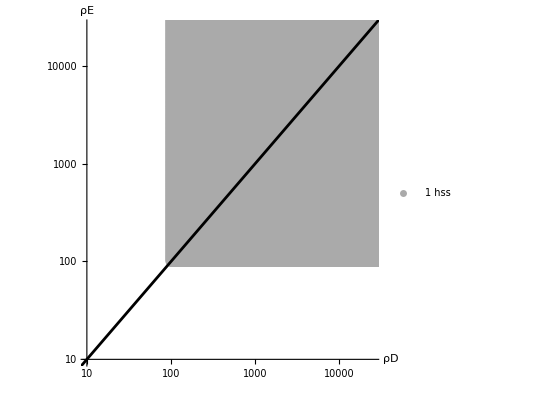

```mathematica
Show[ListLogLogPlot[DeleteCases[{{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,-2]]==1&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,-2]]==2&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,-2]]==3&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,-2]]==4&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,-2]]==5&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASwitch,#[[2,-2]]==6&]},{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"ρD","ρE"}),AspectRatio->1,TicksStyle->Directive[14],AxesStyle->Thickness[0.002],
PlotRange->{{10,25000},{10,25000}},
PlotLegends->((#[[1]]&/@DeleteCases[{#[[2,-2]]&/@Select[sweepLSASwitch,#[[2,-2]]==1&],#[[2,-2]]&/@Select[sweepLSASwitch,#[[2,-2]]==2&],#[[2,-2]]&/@Select[sweepLSASwitch,#[[2,-2]]==3&],#[[2,-2]]&/@Select[sweepLSASwitch,#[[2,-2]]==4&],#[[2,-2]]&/@Select[sweepLSASwitch,#[[2,-2]]==5&],#[[2,-2]]&/@Select[sweepLSASwitch,#[[2,-2]]==6&]},{}])/.{1->"1 hss",2->"2 hss, one locally stable",3->"2 hss, both locally stable",4->"2 hss, both locally unstable",5->"3 hss",6->"more than 3 hss"})],Plot[rho,{rho,0,10000},PlotStyle->Black]]
```

```mathematica
sweepLSASwitch2=Transpose@Partition[sweepLSASwitch,Length[Range[2,4.5,0.01]]];
```

```mathematica
boundarySwitch=Last@Last@Reap@Do[Block[{evals,bnds},
evals={#[[1,1]],Function[x,If[Length[x]>1,If[x[[1,1]]==1,Max[x[[2;;,-1]]],Max[x[[All,-1]]]],x[[-1,-1]]]]@FindPeaks[Re@#[[2,2,All,2,-1]],0]}&/@disps;
bnds=DeleteCases[MovingMap[
Block[{
min,
max,
ind
},
{min,max}=SortBy[Transpose[{{1,2},#1}],Function[x,x[[2]]]][[All,1]];
If[(#1[[min]]<10^-10)&&(#1[[max]]>10^-10),Mean[#2],None]
]&,
evals,Quantity[2,"Events"]][[All,2]],None];
Print[bnds];
If[Length@bnds>0,
Sow[{#,disps[[1,1,2]]}&/@bnds]]
],{disps,sweepLSASwitch2}];
```

{}

{}

{}

«61 more identical outputs»

{1603.35,1640.7}

{1428.99,1883.77}

{1333.61,2018.5}

{1273.59,2162.86}

{1244.6,2264.79}

{1216.27,2317.55}

{1188.58,2426.77}

{1161.53,2483.3}

{1135.09,2600.33}

{1109.25,2660.9}

{1084.,2786.31}

{1059.32,2851.21}

{1059.32,2917.62}

{1035.21,2985.58}

{1011.65,3055.12}

{1011.65,3199.11}

{988.619,3273.62}

{988.619,3349.88}

{966.115,3427.91}

{966.115,3507.75}

{944.123,3589.46}

{944.123,3673.07}

{944.123,3758.62}

{922.633,3846.17}

{922.633,3935.76}

{901.631,4027.44}

{901.631,4121.25}

{901.631,4121.25}

{901.631,4217.24}

{881.107,4315.48}

{881.107,4416.}

{881.107,4518.86}

{861.051,4624.12}

{861.051,4731.83}

{861.051,4842.04}

{861.051,4954.83}

{861.051,5188.34}

{841.451,5309.2}

{841.451,5432.86}

{841.451,5559.41}

{841.451,5688.91}

{841.451,5821.42}

{841.451,5957.02}

{841.451,6095.77}

{822.297,6237.76}

{822.297,6383.06}

{822.297,6531.74}

{822.297,6683.88}

{822.297,6839.57}

{822.297,6998.88}

{822.297,6998.88}

{822.297,7161.91}

{822.297,7328.73}

{822.297,7499.44}

{822.297,7674.12}

{822.297,7852.88}

{822.297,8035.79}

{822.297,8222.97}

{822.297,8222.97}

{822.297,8414.51}

{822.297,8610.51}

{822.297,8811.07}

{822.297,9016.31}

{822.297,9226.33}

{822.297,9226.33}

{822.297,9441.23}

{822.297,9661.15}

{822.297,9886.19}

{822.297,10116.5}

{822.297,10352.1}

{841.451,10352.1}

{841.451,10593.2}

{841.451,10840.}

{841.451,11092.5}

{841.451,11350.9}

{841.451,11350.9}

{841.451,11615.3}

{861.051,11885.8}

{861.051,12162.7}

{861.051,12162.7}

{861.051,12446.}

{861.051,12735.9}

{881.107,13032.5}

{881.107,13336.1}

{881.107,13336.1}

{881.107,13646.7}

{881.107,13964.6}

{901.631,14289.9}

{901.631,14289.9}

{901.631,14622.7}

{901.631,14963.3}

{922.633,15311.9}

{922.633,15311.9}

{922.633,15668.5}

{922.633,16033.5}

{944.123,16407.}

{944.123,16407.}

{944.123,16789.2}

{966.115,17180.2}

{966.115,17580.4}

{966.115,17580.4}

{988.619,17989.9}

{988.619,18408.9}

{988.619,18837.7}

{1011.65,18837.7}

{1011.65,19276.5}

{1035.21,19725.5}

{1035.21,20185.}

{1035.21,20185.}

{1059.32,20655.2}

{1059.32,21136.3}

{1084.,21628.6}

{1084.,21628.6}

{1084.,22132.4}

{1109.25,22647.9}

{1109.25,22647.9}

{1135.09,23175.5}

{1135.09,23715.3}

{1161.53,24267.7}

{1161.53,24267.7}

{1188.58,24833.}

{1188.58,25411.4}

{1216.27,26003.3}

{1216.27,26003.3}

{1216.27,26609.}

{1244.6,27228.8}

{1273.59,27863.1}

{1273.59,27863.1}

{1303.25,28512.1}

{1303.25,29176.2}

{1333.61,29855.8}

{1333.61,29855.8}

{1364.67,30551.2}

{1364.67,31262.9}

{1396.46,31262.9}

{1396.46}

{1428.99}

{1462.27}

{1462.27}

{1496.33}

{1496.33}

{1531.19}

{1566.85}

{1566.85}

{1603.35}

{1603.35}

{1640.7}

{1678.92}

{1678.92}

{1718.02}

{1758.04}

{1758.04}

{1798.99}

{1840.89}

{1840.89}

{1883.77}

{1927.65}

{1927.65}

{1972.55}

{2018.5}

{2018.5}

{2065.52}

{2113.63}

{2162.86}

{2162.86}

{2213.24}

{2264.79}

{2264.79}

{2317.55}

{2371.53}

{2426.77}

{2426.77}

{2483.3}

{2541.14}

{2600.33}

{2600.33}

{2660.9}

{2722.88}

{2786.31}

{2851.21}

{2851.21}

{2917.62}

{2985.58}

{3055.12}

{3126.29}

{3126.29}

{3199.11}

```mathematica
boundarySwitchCont=Join[Reverse@#[[All,1]],SortBy[Complement[Flatten[#,1],#[[All,1]]],Function[x,x[[2]]]]]&@boundarySwitch;
```

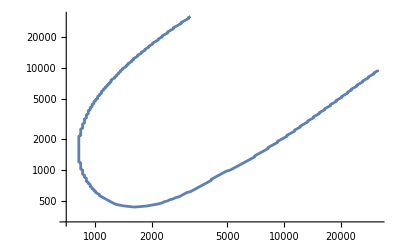

```mathematica
ListLogLogPlot[boundarySwitchCont,Joined->True]
```

### Skeleton model

```mathematica
Monitor[sweepLSASkeletonScaled30=Table[
{
rho,
testInstab[Join[{rhoD->rho[[1]]/4,rhoE->rho[[2]]/4},DeleteCases[paramsSkeletonScaled,(rhoD->_)|(rhoE->_)]]]
},{rho,Flatten[Outer[List,10^Range[2,4.35,0.02],10^Range[2,4.3,0.02]],1]}];,rho]
```

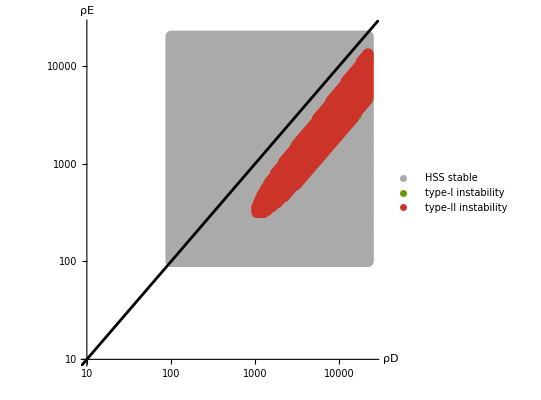

```mathematica
Show[ListLogLogPlot[DeleteCases[{{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==0&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==1&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==2&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==3&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==4&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==5&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==6&]},{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"ρD","ρE"}),AspectRatio->1,TicksStyle->Directive[14],AxesStyle->Thickness[0.002],
PlotRange->{{10,25000},{10,25000}},PlotLegends->((#[[1]]&/@DeleteCases[{#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==0&],#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==1&],#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==2&],#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==3&],#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==4&],#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==5&],#[[2,1]]&/@Select[sweepLSASkeletonScaled30,#[[2,1]]==6&]},{}])/.{0->"HSS stable",1->"type-III instability",2->"type-III + type-I instability with σ<0 in between",3->"type-I + type-III instability with σ>0 for q<qc",4->"type-I + type-III instability with σ<0 for q<qc",5->"type-I instability",6->"type-II instability"})],Plot[rho,{rho,0,10000},PlotStyle->Black]]
```

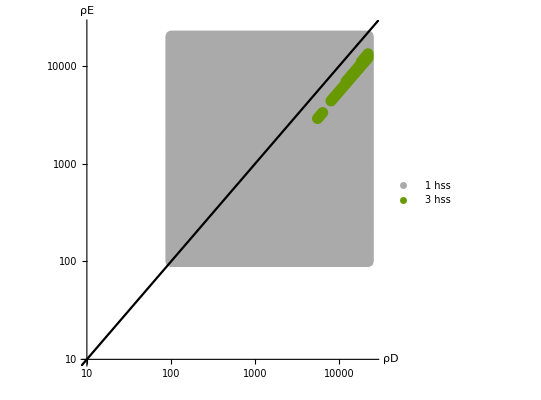

```mathematica
Show[ListLogLogPlot[DeleteCases[{{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==1&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==2&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==3&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==4&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==5&],{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==6&]},{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"ρD","ρE"}),AspectRatio->1,TicksStyle->Directive[14],AxesStyle->Thickness[0.002],
PlotRange->{{10,25000},{10,25000}},
PlotLegends->((#[[1]]&/@DeleteCases[{#[[2,-2]]&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==1&],#[[2,-2]]&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==2&],#[[2,-2]]&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==3&],#[[2,-2]]&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==4&],#[[2,-2]]&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==5&],#[[2,-2]]&/@Select[sweepLSASkeletonScaled30,#[[2,-2]]==6&]},{}])/.{1->"1 hss",2->"2 hss, one locally stable",3->"2 hss, both locally stable",4->"2 hss, both locally unstable",5->"3 hss",6->"more than 3 hss"})],Plot[rho,{rho,0,10000},PlotStyle->Black]]
```

```mathematica
sweepLSASkeletonScaled2=Transpose@Partition[sweepLSASkeletonScaled30,Length[Range[2,4.3,0.02]]];
```

```mathematica
boundarySkeleton=Last@Last@Reap@Do[Block[{evals,bnds},
evals={#[[1,1]],Function[x,If[Length[x]>1,If[x[[1,1]]==1,Max[x[[2;;,-1]]],Max[x[[All,-1]]]],x[[-1,-1]]]]@FindPeaks[Re@#[[2,2,All,2,-1]],0]}&/@disps;
bnds=DeleteCases[MovingMap[
Block[{
min,
max,
ind
},
{min,max}=SortBy[Transpose[{{1,2},#1}],Function[x,x[[2]]]][[All,1]];
If[(#1[[min]]<10^-10)&&(#1[[max]]>10^-10),Mean[#2],None]
]&,
evals,Quantity[2,"Events"]][[All,2]],None];
Print[bnds];
If[Length@bnds>0,
Sow[{#,disps[[1,1,2]]}&/@bnds]]
],{disps,sweepLSASkeletonScaled2}];
```

{}

{}

{}

«22 more identical outputs»

{1023.56,1288.59}

{1023.56,1412.91}

{1023.56,1479.5}

{1023.56,1622.24}

{1071.8,1698.69}

{1071.8,1862.58}

{1122.32,1950.36}

{1122.32,2042.28}

{1175.21,2239.31}

{1175.21,2344.85}

{1230.59,2455.36}

{1288.59,2571.08}

{1288.59,2692.25}

{1349.32,2819.13}

{1412.91,3091.11}

{1412.91,3236.79}

{1479.5,3389.34}

{1549.23,3549.07}

{1622.24,3716.34}

{1698.69,3891.48}

{1698.69,4074.88}

{1778.75,4266.93}

{1862.58,4468.02}

{1950.36,4678.59}

{2042.28,4899.09}

{2138.53,5129.97}

{2138.53,5371.74}

{2239.31,5624.9}

{2344.85,5890.}

{2455.36,6167.58}

{2571.08,6458.25}

{2692.25,6762.62}

{2819.13,7081.33}

{2951.99,7415.07}

{2951.99,7764.53}

{3091.11,8130.46}

{3236.79,8513.64}

{3389.34,8914.87}

{3549.07,9335.02}

{3716.34,9774.96}

{3891.48,10235.6}

{4074.88,10718.}

{4266.93,11223.2}

{4468.02,11752.1}

{4678.59,12305.9}

{4899.09,12885.9}

{5129.97,13493.2}

{5371.74,14129.1}

{5371.74,14795.}

{5624.9,15492.3}

{5890.,16222.4}

{6167.58,16222.4}

{6458.25,16986.9}

{6762.62,17787.5}

{7081.33,18625.8}

{7415.07,19503.6}

{7764.53,20422.8}

{7764.53,21385.3}

{8130.46}

{8513.64}

{8914.87}

{9335.02}

{9774.96}

{10235.6}

{10718.}

{11223.2}

{11752.1}

{11752.1}

{12305.9}

{12885.9}

{13493.2}

{14129.1}

{14795.}

{15492.3}

{16222.4}

{16986.9}

{17787.5}

{17787.5}

{18625.8}

{19503.6}

{20422.8}

{21385.3}

{}

{}

{}

«6 more identical outputs»

```mathematica
boundarySkeletonCont=Join[Reverse@#[[All,1]],SortBy[Complement[Flatten[#,1],#[[All,1]]],Function[x,x[[2]]]]]&@boundarySkeleton;
```

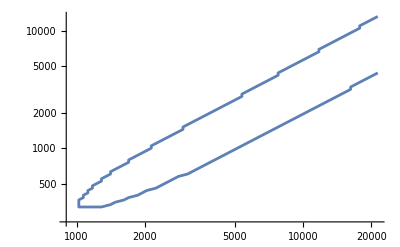

```mathematica
ListLogLogPlot[boundarySkeletonCont,Joined->True]
```

### Results

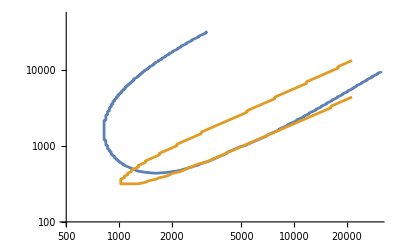

```mathematica
ListLogLogPlot[{boundarySwitchCont,boundarySkeletonCont},Joined->True,PlotRange->{{500,30000},{100,50000}}]
```